```mathematica
ClearAll["Global`*"];
u = 1.0; 
mu = 1.0;
a  = 1.4;
b  = 1.4;

C0 = u/mu;
S0 = (a/b) C0;
tc = 1/mu;

scalesTable = Grid[{ {"Scale", "Definition", "Value"},{"C0", "u/mu", N[C0]},
    {"S0", "(a/b) C0", N[S0]},{"tc", "1/mu", N[tc]} },
  Frame -> All, Alignment -> Left];
```

```mathematica
scalesTable
```

Scale | Definition | Value
C0 | u/mu | 1.
S0 | (a/b) C0 | 1.
tc | 1/mu | 1.

```mathematica
(*x(t)=Crowding,y(t)=Stress,z(t)=Adoption*)
(* Choose device/adoption parameters (dimensionless) *)
gammaVal = 0.9;    (* device coupling strength *)
deltaVal = 1.2;    (* adoption growth from stress *)
epsVal   = 0.25;   (* adoption decay *)

(* Derived alpha, beta from the scales above *)
alphaVal = N[a C0/(mu S0)];
betaVal  = N[b/mu];

paramTable = Grid[
  {
    {"Parameter", "Definition", "Value"},
    {"alpha", "a C0/(mu S0)", alphaVal},
    {"beta",  "b/mu",        betaVal},
    {"gamma", "k/mu",        gammaVal},
    {"delta", "p S0/mu",     deltaVal},
    {"epsilon", "q/mu",      epsVal}
  },
  Frame -> All, Alignment -> Left];
paramTable
```

Parameter | Definition | Value
alpha | a C0/(mu S0) | 1.4
beta | b/mu | 1.4
gamma | k/mu | 0.9
delta | p S0/mu | 1.2
epsilon | q/mu | 0.25

```mathematica
(* Baseline steady stress when gamma=0 *)
yStarNoDev = N[alphaVal/betaVal];
zStarNoDev = N[(deltaVal yStarNoDev)/(deltaVal yStarNoDev + epsVal)];

(* With device: solve two equations in y,z *)
eqYZ[gam_?NumericQ] := {
  y == alphaVal/(betaVal + gam z),
  z == (deltaVal y)/(deltaVal y + epsVal)};
solveYZ[gam_?NumericQ] := Module[{sol},
  sol = FindRoot[eqYZ[gam], {{y, yStarNoDev}, {z, zStarNoDev}}];
  {N[y /. sol], N[z /. sol]}];

{yStarDev, zStarDev} = solveYZ[gammaVal];

inequalityText = Grid[{
    {"Baseline (gamma=0) steady stress", "y0* = alpha/beta", yStarNoDev},
    {"With device (gamma>0) steady stress", "y* = alpha/(beta + gamma z*)", yStarDev},
    {"Check", "y* < y0* ?", yStarDev < yStarNoDev}},
  Frame -> All, Alignment -> Left];
```

```mathematica
inequalityText
```

Baseline (gamma=0) steady stress | y0* = alpha/beta | 1.
With device (gamma>0) steady stress | y* = alpha/(beta + gamma z*) | 0.670901
Check | y* < y0* ? | True

```mathematica
tMax = 20.0;
x0 = 0.2; y0 = 0.1; z0 = 0.0;

f[{xx_, yy_, zz_}, gam_] := {
  1 - xx,
  alphaVal xx - betaVal yy - gam yy zz,
  deltaVal yy (1 - zz) - epsVal zz};

(* Build equations as a function of gamma so gamma=0 truly changes the model *)
eqsND[gam_?NumericQ] := {
  x'[tau] == 1 - x[tau],
  y'[tau] == alphaVal x[tau] - betaVal y[tau] - gam y[tau] z[tau],
  z'[tau] == deltaVal y[tau] (1 - z[tau]) - epsVal z[tau],
  x[0] == x0, y[0] == y0, z[0] == z0};

solNoDev = NDSolveValue[eqsND[0.0], {x, y, z}, {tau, 0, tMax}];
solDev   = NDSolveValue[eqsND[gammaVal], {x, y, z}, {tau, 0, tMax}];

xNoDev[t_] := solNoDev[[1]][t];
yNoDev[t_] := solNoDev[[2]][t];
zNoDev[t_] := solNoDev[[3]][t];

xDev[t_] := solDev[[1]][t];
yDev[t_] := solDev[[2]][t];
zDev[t_] := solDev[[3]][t];
```

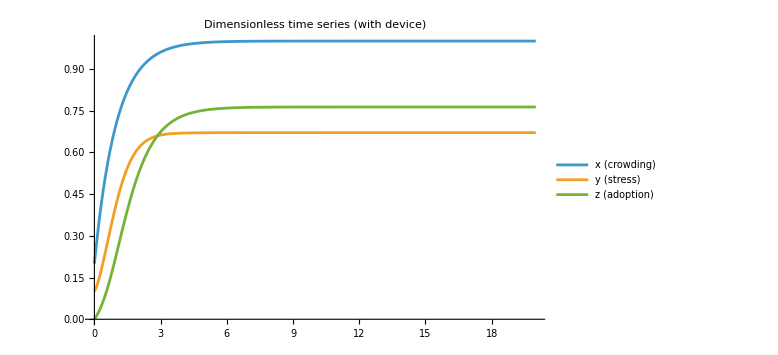

```mathematica
pNDTime = Plot[
  Evaluate@{xDev[tau], yDev[tau], zDev[tau]},
  {tau, 0, tMax},
  PlotRange -> All, ImageSize -> Large,
  PlotLegends -> {"x (crowding)", "y (stress)", "z (adoption)"},
  PlotLabel -> "Dimensionless time series (with device)"];
pNDTime
```

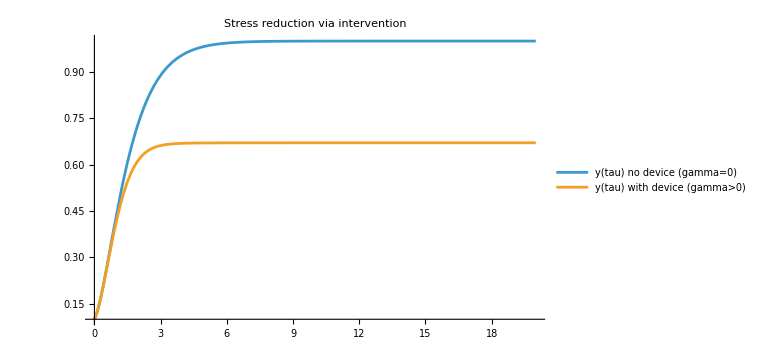

```mathematica
pStressCompare = Plot[
  Evaluate@{yNoDev[tau], yDev[tau]},
  {tau, 0, tMax},
  PlotRange -> All, ImageSize -> Large,
  PlotLegends -> {"y(tau) no device (gamma=0)", "y(tau) with device (gamma>0)"},
  PlotLabel -> "Stress reduction via intervention"];
pStressCompare
```

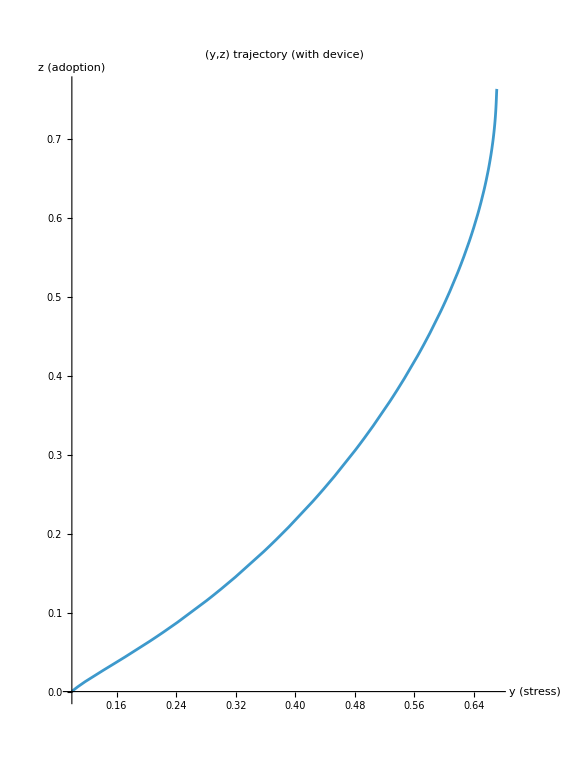

```mathematica
pYZ = ParametricPlot[
  Evaluate@{yDev[tau], zDev[tau]},
  {tau, 0, tMax},
  PlotRange -> All, ImageSize -> Large,
  AxesLabel -> {"y (stress)", "z (adoption)"},
  PlotLabel -> "(y,z) trajectory (with device)"];
pYZ
```

```mathematica
(*ensure numeric parameters*)
alphaVal=1.4;
betaVal=1.4;
deltaVal=1.2;
epsVal=0.25;
gammaVal=0.9;

(*equilibrium:no device*)
xStar=1.0;
yStarNoDev=alphaVal/betaVal;
zStarNoDev=deltaVal*yStarNoDev/(deltaVal*yStarNoDev+epsVal);

(*equilibrium:with device (numeric)*)
rootDevEq=FindRoot[{alphaVal-betaVal y-gammaVal y z==0,deltaVal y (1-z)-epsVal z==0},{{y,yStarNoDev},{z,zStarNoDev}},MaxIterations->200];

{yStarDev,zStarDev}={y,z}/. rootDevEq;

(*Jacobian*)
Jmat[xx_,yy_,zz_,gam_]:={{-1,0,0},{alphaVal,-(betaVal+gam zz),-(gam yy)},{0,deltaVal (1-zz),-(deltaVal yy+epsVal)}};

eigNoDev=Chop@N@Eigenvalues[Jmat[xStar,yStarNoDev,zStarNoDev,0.0]];
eigDev=Chop@N@Eigenvalues[Jmat[xStar,yStarDev,zStarDev,gammaVal]];

stabilityTable=Grid[{{"Case","Equilibrium (x*,y*,z*)","Eigenvalues (approx)"},{"No device (gamma=0)",{xStar,yStarNoDev,zStarNoDev},eigNoDev},{"With device (gamma>0)",{xStar,yStarDev,zStarDev},eigDev}},Frame->All,Alignment->Left];
stabilityTable
```

Case | Equilibrium (x*,y*,z*) | Eigenvalues (approx)
No device (gamma=0) | {1.,1.,0.827586} | {-1.45,-1.4,-1.}
With device (gamma>0) | {1.,0.670901,0.763051} | {-1.87815,-1.26367,-1.}

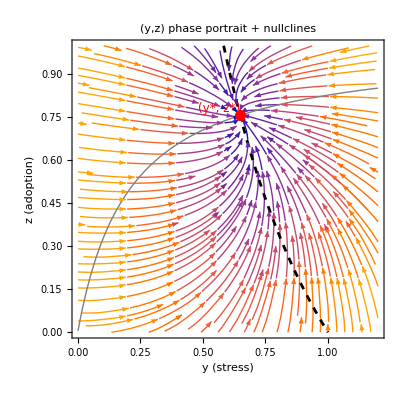

```mathematica
(*(y,z) phase portrait+nullclines*)fYZ[gam_][y_,z_]:={alphaVal-betaVal y-gam y z,deltaVal y (1-z)-epsVal z };

(*equilibrium in (y,z) for given gam*)
yzStar[gam_?NumericQ]:=Module[{sol},If[gam==0,{alphaVal/betaVal,(deltaVal (alphaVal/betaVal))/(deltaVal (alphaVal/betaVal)+epsVal)},sol=FindRoot[{alphaVal-betaVal y-gam y z==0,deltaVal y (1-z)-epsVal z==0},{{y,alphaVal/betaVal},{z,0.5}},MaxIterations->200];
{y,z}/. sol]];

gamPlot=1.0;  (*with device;change to 0 for no-device*)
{yS,zS}=yzStar[gamPlot];

yMax=1.2 (alphaVal/betaVal); 
zMax=1.0;

Show[StreamPlot[Evaluate[fYZ[gamPlot][y,z]],{y,0.001,yMax},{z,0,zMax},StreamPoints->Fine,StreamScale->Medium,PlotLabel->"(y,z) phase portrait + nullclines",FrameLabel->{"y (stress)","z (adoption)"}],ContourPlot[Evaluate[First@fYZ[gamPlot][y,z]==0],{y,0.001,yMax},{z,0,zMax},Contours->{0},ContourStyle->Directive[Black,Dashed]],ContourPlot[Evaluate[Last@fYZ[gamPlot][y,z]==0],{y,0.001,yMax},{z,0,zMax},Contours->{0},ContourStyle->Directive[Gray,Thick]],Graphics[{Red,PointSize[0.02],Point[{yS,zS}],Text[Style["(y*, z*)",12,Red],{yS,zS},{1,-1}]}]]
```

Check y*(0) = 1.   alpha/beta = 1.

Check y*(2) = 0.498177

Data points = 41, first/last = {0.,1.}  {2.,0.498177}

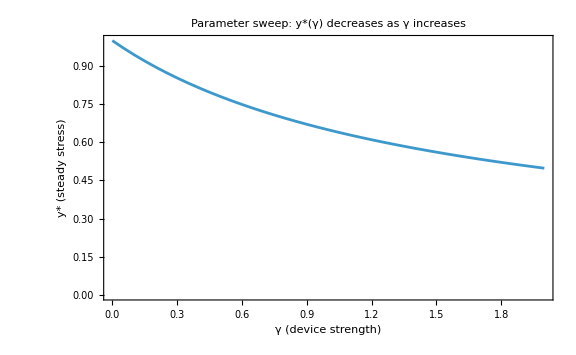

```mathematica
(*Parameter sweep (robust,analytic) y*(gamma) should decrease with gamma*)
ClearAll[yStarFromGamma,zStarFromGamma,gammaVals,yStarData,pSweep];


yStarFromGamma[gam_?NumericQ]:=Module[{A,B,C,disc,r1,r2},A=deltaVal (betaVal+gam);
B=betaVal epsVal-alphaVal deltaVal;
C=-alphaVal epsVal;
disc=B^2-4 A C;
If[disc<0,Return[Missing["NoRealRoot"]]];
r1=(-B+Sqrt[disc])/(2 A);
r2=(-B-Sqrt[disc])/(2 A);
SelectFirst[{r1,r2},#>0&,Missing["NoPositiveRoot"]]];

zStarFromGamma[gam_?NumericQ]:=Module[{y=yStarFromGamma[gam]},If[MissingQ[y],y,N[deltaVal y/(deltaVal y+epsVal)]]];


Print["Check y*(0) = ",yStarFromGamma[0.],"   alpha/beta = ",N[alphaVal/betaVal]];
Print["Check y*(2) = ",yStarFromGamma[2.]];

(*4) 扫描并画图*)
gammaVals=Range[0,2,0.05];

yStarData=Select[({#,yStarFromGamma[#]}&)/@gammaVals,NumericQ[Last[#]]&];

Print["Data points = ",Length[yStarData],", first/last = ",First[yStarData],"  ",Last[yStarData]];

pSweep=ListLinePlot[yStarData,Frame->True,FrameLabel->{"γ (device strength)","y* (steady stress)"},PlotRange->All,ImageSize->Large,PlotLabel->"Parameter sweep: y*(γ) decreases as γ increases"];
pSweep
```

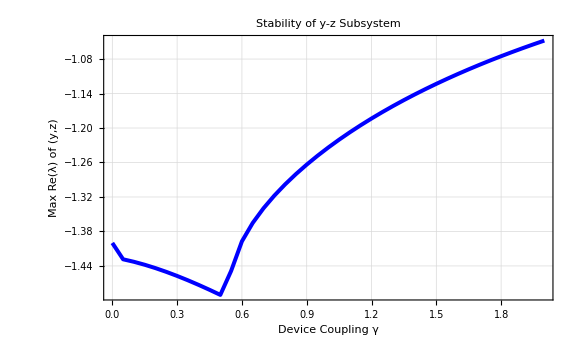

```mathematica
(*Stability analysis (for y-z subsystem)*)
(*only considering the interaction between y and z,the interference from the-1 eigenvalue of x is eliminated.*)Jyz[gam_,y_,z_]:={{-betaVal-gam*z,-gam*y},{deltaVal*(1-z),-deltaVal*y-epsVal}};


eigDataYZ=Table[Module[{gam,yS,zS,evals},gam=row[[1]];yS=row[[2]];zS=(deltaVal*yS)/(deltaVal*yS+epsVal);
evals=Eigenvalues[Jyz[gam,yS,zS]];
{gam,Max[Re[evals]]}],{row,yStarData} ];


ListLinePlot[eigDataYZ,Frame->True,FrameLabel->{"Device Coupling γ","Max Re(λ) of (y,z)"},PlotLabel->"Stability of y-z Subsystem",PlotStyle->{Blue,Thickness[0.005]},Epilog->{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->Large,GridLines->Automatic]
```

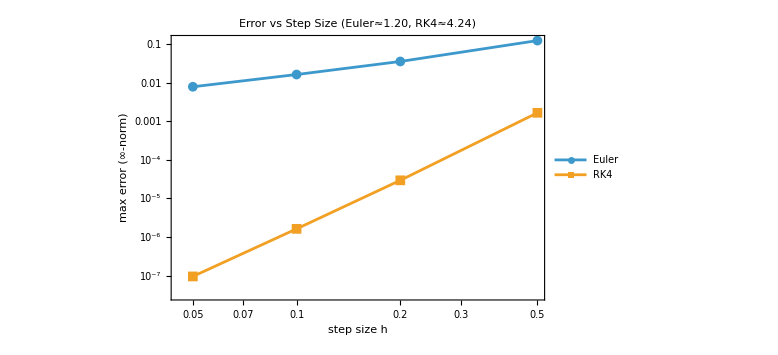

Method | Expected order | Observed order (approx)
Euler | 1 | 1.20
RK4 | 4 | 4.24

```mathematica
ClearAll[rhs,tGrid,eulerSim,rk4Sim,refSol,maxErrY,slopeOrder,hList,tMax,s0,dataEuler,dataRK4,ordEuler,ordRK4,pErr,orderTable,wp,alphaP,betaP,deltaP,epsP,gammaP,s0P,tMaxP];


If[!And@@(NumericQ/@{alphaVal,betaVal,deltaVal,epsVal,gammaVal}),Print["ERROR: alphaVal/betaVal/deltaVal/epsVal/gammaVal are not numeric."];
Abort[];];

(*use consistent high precision for reference to avoid precw*)
wp=40;
alphaP=SetPrecision[alphaVal,wp];
betaP=SetPrecision[betaVal,wp];
deltaP=SetPrecision[deltaVal,wp];
epsP=SetPrecision[epsVal,wp];
gammaP=SetPrecision[gammaVal,wp];

tMax=20;
tMaxP=SetPrecision[tMax,wp];

(*use exact rational steps to avoid out-of-range/rounding issues*)
hList={1/2,1/5,1/10,1/20};   

s0={0.2,0.1,0.0};
s0P=SetPrecision[s0,wp];

rhs[{x_,y_,z_},gam_]:={1-x,alphaVal x-betaVal y-gam y z,deltaVal y (1-z)-epsVal z};

tGrid[tmax_,h_]:=Range[0,tmax,h];

eulerSim[gam_,h_,tmax_,sInit_]:=Module[{ts,n,states},ts=tGrid[tmax,h];
n=Length[ts]-1;
states=NestList[#+h rhs[#,gam]&,sInit,n];
Transpose[{N@ts,N@states}]];

rk4Sim[gam_,h_,tmax_,sInit_]:=Module[{ts,n,step},ts=tGrid[tmax,h];
n=Length[ts]-1;
step[s_]:=Module[{k1,k2,k3,k4},k1=rhs[s,gam];
k2=rhs[s+(h/2) k1,gam];
k3=rhs[s+(h/2) k2,gam];
k4=rhs[s+h k3,gam];
s+(h/6) (k1+2 k2+2 k3+k4)];
Transpose[{N@ts,N@NestList[step,sInit,n]}]];

(*high-accuracy reference (same Phase 2 ODE),all in wp precision*)
refSol=Quiet@NDSolveValue[{x'[t]==1-x[t],y'[t]==alphaP x[t]-betaP y[t]-gammaP y[t] z[t],z'[t]==deltaP y[t] (1-z[t])-epsP z[t],x[0]==s0P[[1]],y[0]==s0P[[2]],z[0]==s0P[[3]]},{x,y,z},{t,0,tMaxP},Method->"StiffnessSwitching",WorkingPrecision->wp,AccuracyGoal->20,PrecisionGoal->20,MaxStepSize->SetPrecision[tMax/5000,wp]];

maxErrY[simFun_,h_]:=Module[{traj,ts,ySim,yTrue,tsP},traj=simFun[gammaVal,N@h,tMax,s0];
ts=traj[[All,1]];
ySim=traj[[All,2,2]];
tsP=SetPrecision[ts,wp];
yTrue=N[refSol[[2]]/@tsP];N@Max@Abs[ySim-yTrue]];

dataEuler=({N@#,maxErrY[eulerSim,#]}&)/@hList;
dataRK4=({N@#,maxErrY[rk4Sim,#]}&)/@hList;

(*slope of log(err) vs log(h),no LinearModelFit*)
slopeOrder[data_List]:=Module[{x,y,n,num,den},x=Log[data[[All,1]]];
y=Log[Clip[data[[All,2]],{$MachineEpsilon,Infinity}]];
n=Length[x];
num=n Total[x y]-Total[x] Total[y];
den=n Total[x^2]-(Total[x])^2;
N[num/den]];

ordEuler=slopeOrder[dataEuler];
ordRK4=slopeOrder[dataRK4];

pErr=ListLogLogPlot[{dataEuler,dataRK4},Joined->True,PlotMarkers->{Automatic,10},Frame->True,FrameLabel->{"step size h","max error (∞-norm)"},PlotLegends->Placed[{"Euler","RK4"},Above],PlotRange->All,ImageSize->Large,PlotLabel->Row[{"Error vs Step Size (Euler≈",NumberForm[ordEuler,{3,2}],", RK4≈",NumberForm[ordRK4,{3,2}],")"}]];

orderTable=Grid[{{"Method","Expected order","Observed order (approx)"},{"Euler",1,NumberForm[ordEuler,{4,2}]},{"RK4",4,NumberForm[ordRK4,{4,2}]}},Frame->All,Alignment->Center];

pErr
orderTable
```